# Simple Task 10

Brian Carlson 3-17-2014

### Task

Write a function rectanglesToFun[fun, {lower, upper}, p], which is given the name of a function, an interval specified by  lower and upper, and a positive integer p. Assume that the given function is increasing over the entire interval. The function rectanglesToFun  draws p rectangles evenly spaced over the interval [lower,upper].  Each rectangle contain two sides parallel to the y-axis and two sides parallel to the x-axis. The rectangles should be completely between the function and the x-axis. Your code must show the function (extended more than the distances between the lines beyond lower and upper to show that you are not plotting too many times) as well as the rectangles.

### Solution

```mathematica
rectanglesToFun[fun_,{lower_,upper_},p_]:=Module[{c=(upper-lower)/p},(*creates the increment*)Show[{Plot[fun[x],{x,lower-2c,upper+2c},(*Plots our graph*)PlotRange->{fun[lower]-1,fun[upper]+1}],Graphics[Prepend[Table[Rectangle[{i+c,0},{i,fun[i]}],{i,lower,upper-c,c}],(*Prepares our table of rectangles*)Directive[EdgeForm[{Thick,Red}],White]]]}]]
```

#### Test Cases

```mathematica
testFun[x_] :=  E^(0.5x)+ .5(20+x)^(1/2)
f[x_] :=x-3
```

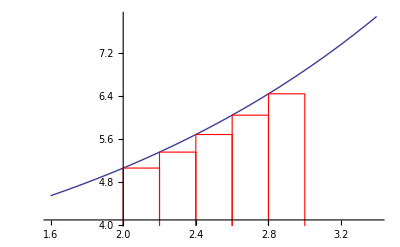

```mathematica
rectanglesToFun[testFun,{2,3},5]
```

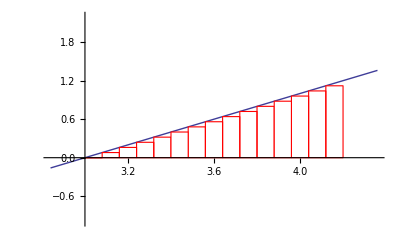

```mathematica
rectanglesToFun[f,{3,4.2},15]
```

```mathematica
Manipulate[rectanglesToFun[testFun, {-1, 6}, k],{k,2,Infinity}]
```

### Solution For all Values

```mathematica
rectanglesToFun2[fun_,{lower_,upper_},p_]:=Module[{c=(upper-lower)/p,root=x/.FindRoot[fun[x],{x,lower}]},(*creates the increment, finds the root*)Show[{Plot[fun[x],{x,lower-2c,upper+2c},(*Plots our graph*)PlotRange->{fun[lower]-1,fun[upper]+1}],Graphics[Prepend[Table[Rectangle[{i+c,0},(*Prepares our table of rectangles*){i,If[IntervalMemberQ[Interval[{i,i+c}],root],0,(*Catches negative values and zeros*)If[fun[i]≤ 0,fun[i+c],fun[i]]]}],{i,lower,upper-c,c}],Directive[EdgeForm[{Thick,Red}],White]]]}]]
```

#### Test Cases

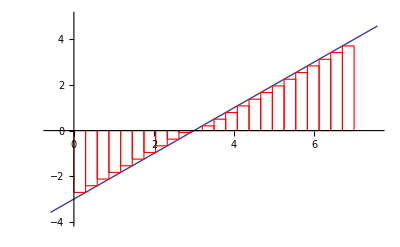

```mathematica
rectanglesToFun2[f,{0,7},24]
```

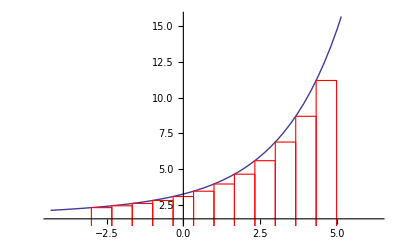

```mathematica
rectanglesToFun2[testFun,{-3,5},12]
```

```mathematica
Manipulate[rectanglesToFun2[f,{-2,7},k],{k,1,Infinity}]
```